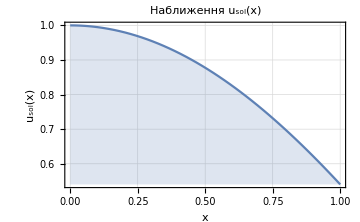
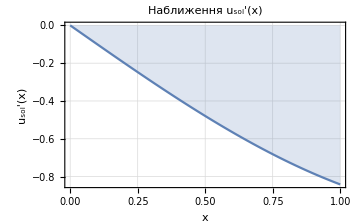

‖u_sol‖_0=0.852833												‖u_sol‖_1=1.

################################################[----FEM n=10 h=1/10 t=t_begin----]################################################

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression 1+i cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at x = 1..

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression 1+i cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at x = 1..

M=(0.0666667 | 0.0166667 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0166667 | 0.0666667 | 0.0166667 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0166667 | 0.0666667 | 0.0166667 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0166667 | 0.0666667 | 0.0166667 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.0166667 | 0.0666667 | 0.0166667 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.0166667 | 0.0666667 | 0.0166667 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.0166667 | 0.0666667 | 0.0166667 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0166667 | 0.0666667 | 0.0166667 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0166667 | 0.0666667 | 0.0166667
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0166667 | 0.0333333)

A=(20. | -10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-10. | 20. | -10. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -10. | 20. | -10. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -10. | 20. | -10. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -10. | 20. | -10. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -10. | 20. | -10. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -10. | 20. | -10. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -10. | 20. | -10. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -10. | 20. | -10.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -10. | 10.)

M+Θ*△t*A=(0.0766667 | 0.0116667 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0116667 | 0.0766667 | 0.0116667 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0116667 | 0.0766667 | 0.0116667 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0116667 | 0.0766667 | 0.0116667 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.0116667 | 0.0766667 | 0.0116667 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.0116667 | 0.0766667 | 0.0116667 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.0116667 | 0.0766667 | 0.0116667 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0116667 | 0.0766667 | 0.0116667 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0116667 | 0.0766667 | 0.0116667
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0116667 | 0.0383333)

F={0.124073,0.12221,0.119127,0.114853,0.109431,0.102916,0.0953728,0.0868766,0.0775123,-0.804352}

q={0.014802,0.0171966,0.00737026,-0.0143688,-0.0475931,-0.0917605,-0.14622,-0.210216,-0.2829,-0.363335}

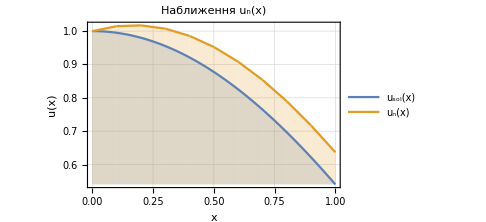
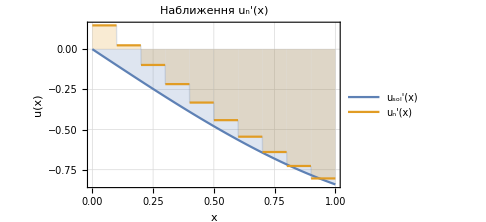

‖u_h‖_0=0.913706 ‖u-u_h‖_0=0.327923 ((‖u - SubscriptBox[u, h]‖)_0)/((‖SubscriptBox[u, h]‖)_0)100%=35.8894%                     ‖u_h‖_1=1.03028 ‖u-u_h‖_1=0.247961 ((‖u - SubscriptBox[u, h]‖)_1)/((‖SubscriptBox[u, h]‖)_1)100%=24.0673%

```mathematica
a=0;b=1;
μ[x_]:=1;β[x_]:=0;σ[x_]:=0;
u0 = Cos[0]; u1 = -Sin[1]; Θ=1/2;
ψ[x_,t_]:=1/(t+1)*Cos[x]; 
uzero[x_]:=Cos[x]+ψ[x,0];
f[x_,t_]:=Cos[x]*(t^2+3*t+1)/(1+t)^2;
ti=1; deltat=1/1000;
n = 10;
$MaxPiecewiseCases=700;
(*Точний розвязок диф рівняння*)
Subscript[u, sol][x_]:=Cos[x];
Subscript[plot1u, sol]=Plot[Subscript[u, sol][x],{x,a,b},FrameLabel->{"x ","u_sol(x) "},PlotLabel->Style[Framed["Наближення u_sol(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Subscript[plot2u, sol]=Plot[Subscript[u, sol]'[x],{x,a,b},FrameLabel->{"x ","u_sol'(x) "},PlotLabel->Style[Framed["Наближення u_sol'(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Subscript[norma1u, sol]=√NIntegrate[Subscript[u, sol][x]^2,{x,a,b}];
Subscript[norma2u, sol]=√NIntegrate[(Subscript[u, sol][x])^2+(Subscript[u, sol]'[x])^2,{x,a,b}];
Print[Subscript[plot1u, sol], "     ", Subscript[plot2u, sol]];
Print["‖u_sol‖_0=",Subscript[norma1u, sol],"\t\t\t\t\t\t\t\t\t\t\t\t‖u_sol‖_1=", Subscript[norma2u, sol]];
(*Функції Куранта*)
ϕ[x0_,i0_] :=
Module[{x=x0, i=i0, k, m},k=i+1; m=i-1;
Piecewise[{
{Piecewise[{{(x-w⟦m⟧)/(w⟦i⟧-w⟦m⟧), w⟦m⟧≤x≤w⟦i⟧},{(w⟦k⟧-x)/(w⟦k⟧-w⟦i⟧),w⟦i⟧≤x≤w⟦k⟧}, {0,x<w⟦i⟧ || x>w⟦k⟧}}],i≠ 1 && i≠n+1}, 
{Piecewise[{{(w⟦k⟧-x)/(w⟦k⟧-w⟦i⟧),w⟦i⟧≤x≤w⟦k⟧},{0,w⟦k⟧<x≤1}}], i==1},
{Piecewise[{{(x-w⟦m⟧)/(w⟦i⟧-w⟦m⟧), w⟦m⟧≤x≤w⟦i⟧},{0,0≤x<w⟦i⟧}}], i==n+1}
}]];
h = (b-a)/n;
w = Table[a+i*h, {i,0,n}];
Print["################################################[----FEM n=",n," h=",h, " t=",Subscript[t, begin],"----]################################################"];
matrixM = 
SparseArray[{{i_,j_}/;Abs[i-j]≤1->
NIntegrate[(ϕ[x,i+1]*ϕ[x,j+1]),
{x,a,b}, Method->"DoubleExponential"]}, {n,n},0.];
matrixA= 
SparseArray[{{i_,j_}/;Abs[i-j]≤1->
NIntegrate[(μ[x]*D[ϕ[x,i+1], x]*D[ϕ[x,j+1], x]+β[x]*D[ϕ[x,i+1], x]*ϕ[x,j+1]+σ[x]*ϕ[x,i+1]*ϕ[x,j+1]),
{x,a,b}, Method->"DoubleExponential"]}, {n,n},0.];
Print["M=",MatrixForm[matrixM]];
Print["A=",MatrixForm[matrixA]];
matrixTotal = matrixM+Θ*deltat*matrixA;
Print["M+Θ*△t*A=",MatrixForm[matrixTotal]];
(*unext[x_]:=u0+deltat*uzero[x];*)
unext[x_]:=∑_(i=0)^n (u0+deltat*uzero[w⟦i+1⟧])*ϕ[x,i+1];
F = Table[NIntegrate[f[x,(ti+(ti+deltat))/2]*ϕ[x,i+1],{x,a,b}]+u1*μ[b]*ϕ[b,i+1]-NIntegrate[(μ[x]*D[unext[x], x]*D[ϕ[x,i+1], x]+β[x]*D[unext[x], x]*ϕ[x,i+1]+σ[x]*unext[x]*ϕ[x,i+1]),
{x,a,b}, Method->"DoubleExponential"], {i,1,n}];
Print["F=",F];
q1 = LinearSolve[matrixA,F];
q2 = LinearSolve[matrixTotal,F];
Print["q=",q1];
Subscript[u, n][x_]:=u0+∑_(i=1)^n q1[[i]]*ϕ[x,i+1];
Subscript[u, n1][x_]:=u0+∑_(i=1)^n q2[[i]]*ϕ[x,i+1];
(*Subscript[u, h][x_]:=∑_(i=0)^n (Subscript[u, n][w⟦i+1⟧]+deltat*uzero[w⟦i+1⟧])*ϕ[x,i+1];*) 
difference1 = Plot[{Subscript[u, sol][x], Subscript[u, n][x]}, {x,a,b}, FrameLabel->{"x ","u(x) "},PlotLegends->"Expressions",PlotLabel->Style[Framed["Наближення u_n(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
difference2 = Plot[{Subscript[u, sol]'[x], Subscript[u, n]'[x]}, {x,a,b}, FrameLabel->{"x ","u(x) "},PlotLegends->"Expressions",PlotLabel->Style[Framed["Наближення u_n'(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Print[difference1, "  ", difference2]; 
Subscript[norma1u, n]=√NIntegrate[Subscript[u, n][x]^2,{x,a,b}];
Subscript[norma2u, n]=√Abs[NIntegrate[(Subscript[u, sol][x]^2),{x,a,b}]-NIntegrate[(Subscript[u, n][x]^2),{x,a,b}]];
Subscript[norma1u, n1]=√NIntegrate[(Subscript[u, n][x])^2+(Subscript[u, n]'[x])^2,{x,a,b}];
Subscript[norma2u, n1]=√Abs[NIntegrate[(Subscript[u, sol][x])^2+(Subscript[u, sol]'[x])^2,{x,a,b}]-NIntegrate[(Subscript[u, n][x])^2+(Subscript[u, n]'[x])^2,{x,a,b}]];
Print["‖u_h‖_0=",Subscript[norma1u, n], " ‖u-u_h‖_0=", Subscript[norma2u, n], " ((‖u - SubscriptBox[u, h]‖)_0)/((‖SubscriptBox[u, h]‖)_0)100%=", (Subscript[norma2u, n]/Subscript[norma1u, n])*100, "%                     ‖u_h‖_1=",Subscript[norma1u, n1], " ‖u-u_h‖_1=", Subscript[norma2u, n1], " ((‖u - SubscriptBox[u, h]‖)_1)/((‖SubscriptBox[u, h]‖)_1)100%=", (Subscript[norma2u, n1]/Subscript[norma1u, n1])*100,"%"];
```